```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA_CT",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs}];
```

## t- t (1-loop - self energy)

```mathematica
tops = CreateTopologies[1,1->1,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,WFCorrections}];
processGGT =  { F[9]}-> {F[9]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8],V[4]}];
```

generic model {Lorentz} initialized

classes model {../../Models/SMS-stop-FA/SMS-stop-FA_CT} initialized

in total: 1 Particles insertion

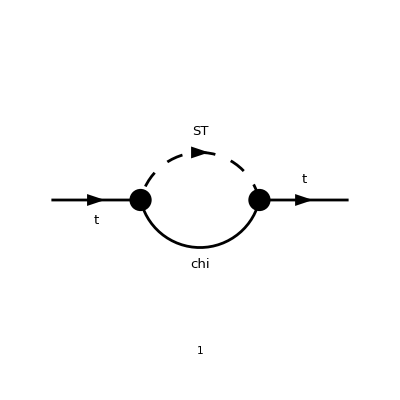

```mathematica
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{1,1},ImageSize->{ 150,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},LorentzIndexNames->{μ,ν},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
```

in total: 1 Particles amplitude

```mathematica
ampC =( TID[ampA,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]);
```

```mathematica
ampC
```

-ⅈ π^2 yDM^2 δ_Col1Col2 (γ·p1).(γ̄)^6 (-((mChi^2-mST^2+p1^2) B_0(p1^2,mChi^2,mST^2))/(2 p1^2)+(A_0(mChi^2))/(2 p1^2)-(A_0(mST^2))/(2 p1^2))

```mathematica
ampE=Simplify[PaXEvaluate[ampC,PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon)]/.{EulerGamma->0,ScaleMu-> ScaleMu/(√(4 Pi))}]
```

-1/(64 π^2 ε p1^4)ⅈ yDM^2 δ_Col1Col2 (γ·p1).(γ̄)^6 (p1^4 (ε log(mChi^2/mST^2)-2 (2 ε+ε log(μ^2/mST^2)+1))+2 ε p1^2 (mChi^2 log(μ^2/(4 mChi^2))-mChi^2 log(μ^2/mST^2)-√(-2 p1^2 (mChi^2+mST^2)+(mChi^2-mST^2)^2+p1^4) log((√(-2 p1^2 (mChi^2+mST^2)+(mChi^2-mST^2)^2+p1^4)+mChi^2+mST^2-p1^2)/(2 mChi mST))+(mChi^2-mST^2) log(mChi^2/mST^2)-mChi^2+mChi^2 log(4 π)-mChi^2 log(π)-mST^2 log(μ^2/(4 π^2 mST^2))+mST^2 log(μ^2/(4 π mST^2))+mST^2-mST^2 log(π))+ε (mChi^2-mST^2) ((mChi^2-mST^2) log(mChi^2/mST^2)-2 √(-2 p1^2 (mChi^2+mST^2)+(mChi^2-mST^2)^2+p1^4) log((√(-2 p1^2 (mChi^2+mST^2)+(mChi^2-mST^2)^2+p1^4)+mChi^2+mST^2-p1^2)/(2 mChi mST))))

## Counter - term (from NLOCT)

Assuming mST >(mChi+MT)

```mathematica
deltaCT=((-I/32)*yDM^2*TensDot[SlashedP[2],ProjP][Index[Spin,Ext[1]],Index[Spin,Ext[2]]])/(Pi^2*ϵ)-((I/32)*yDM^2*Log[μ^2/mST^2]*TensDot[SlashedP[2],ProjP][Index[Spin,Ext[1]],Index[Spin,Ext[2]]])/Pi^2-((I/32)*yDM^2*((2*mChi^2-2*mST^2+MT^2)*(MT*IndexDelta[Index[Spin,Ext[1]],Index[Spin,Ext[2]]]-TensDot[SlashedP[2],ProjM][Index[Spin,Ext[1]],Index[Spin,Ext[2]]])+(-mChi^2+mST^2+MT^2)*TensDot[SlashedP[2],ProjP][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]))/(MT^2*Pi^2)+((I/32)*yDM^2*Log[mChi/mST]*(2*((mChi^2-mST^2)^2-mST^2*MT^2)*(MT*IndexDelta[Index[Spin,Ext[1]],Index[Spin,Ext[2]]]-TensDot[SlashedP[2],ProjM][Index[Spin,Ext[1]],Index[Spin,Ext[2]]])-((mChi^2-mST^2)^2-MT^4)*TensDot[SlashedP[2],ProjP][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]))/(MT^4*Pi^2)-((I/32)*yDM^2*Log[(mChi^2+mST^2-MT^2+Sqrt[mChi^4+(mST^2-MT^2)^2-2*mChi^2*(mST^2+MT^2)])/(2*mChi*mST)]*(-2*(-(mChi^2-mST^2)^3+(mChi^4+mChi^2*mST^2-2*mST^4)*MT^2+mST^2*MT^4)*(MT*IndexDelta[Index[Spin,Ext[1]],Index[Spin,Ext[2]]]-TensDot[SlashedP[2],ProjM][Index[Spin,Ext[1]],Index[Spin,Ext[2]]])+(-mChi^2+mST^2+MT^2)*(mChi^4-2*mChi^2*mST^2+(mST^2-MT^2)^2)*TensDot[SlashedP[2],ProjP][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]))/(MT^4*Sqrt[(mChi-mST-MT)*(mChi+mST-MT)*(mChi-mST+MT)*(mChi+mST+MT)]*Pi^2)/.{IndexDelta[Index[Spin,Ext[1]],Index[Spin,Ext[2]]]->1,TensDot[SlashedP[2],ProjM][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]-> DiracGamma[Momentum[p1,D],D].DiracGamma[7],TensDot[SlashedP[2],ProjP][Index[Spin,Ext[1]],Index[Spin,Ext[2]]]-> DiracGamma[Momentum[p1,D],D].DiracGamma[6]}
```

-(ⅈ yDM^2 ((-mChi^2+mST^2+MT^2) (γ·p1).(γ̄)^6+(2 mChi^2-2 mST^2+MT^2) (MT-(γ·p1).(γ̄)^7)))/(32 π^2 MT^2)+(ⅈ yDM^2 log(mChi/mST) (2 ((mChi^2-mST^2)^2-mST^2 MT^2) (MT-(γ·p1).(γ̄)^7)-((mChi^2-mST^2)^2-MT^4) (γ·p1).(γ̄)^6))/(32 π^2 MT^4)-(ⅈ yDM^2 log((√(-2 mChi^2 (mST^2+MT^2)+mChi^4+(mST^2-MT^2)^2)+mChi^2+mST^2-MT^2)/(2 mChi mST)) ((-mChi^2+mST^2+MT^2) (-2 mChi^2 mST^2+mChi^4+(mST^2-MT^2)^2) (γ·p1).(γ̄)^6-2 (MT^2 (mChi^2 mST^2+mChi^4-2 mST^4)-(mChi^2-mST^2)^3+mST^2 MT^4) (MT-(γ·p1).(γ̄)^7)))/(32 π^2 MT^4 √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)))-(ⅈ yDM^2 log(μ^2/mST^2) (γ·p1).(γ̄)^6)/(32 π^2)-(ⅈ yDM^2 (γ·p1).(γ̄)^6)/(32 π^2 ϵ)

```mathematica
Collect[%32,{Epsilon,Log[a_]}]
```

%32

```mathematica
InputForm[ampE]
```

((-I/64)*yDM^2*DiracGamma[Momentum[p1, D], D] . DiracGamma[6]*
  ((Epsilon*Log[mChi^2/mST^2] - 2*(1 + 2*Epsilon + Epsilon*Log[ScaleMu^2/mST^2]))*
    Pair[Momentum[p1, D], Momentum[p1, D]]^2 + Epsilon*(mChi^2 - mST^2)*
    ((mChi^2 - mST^2)*Log[mChi^2/mST^2] - 
     2*Log[(mChi^2 + mST^2 - Pair[Momentum[p1, D], Momentum[p1, D]] + 
         Sqrt[(mChi^2 - mST^2)^2 - 2*(mChi^2 + mST^2)*Pair[Momentum[p1, D], Momentum[p1, D]] + 
           Pair[Momentum[p1, D], Momentum[p1, D]]^2])/(2*mChi*mST)]*
      Sqrt[(mChi^2 - mST^2)^2 - 2*(mChi^2 + mST^2)*Pair[Momentum[p1, D], Momentum[p1, D]] + 
        Pair[Momentum[p1, D], Momentum[p1, D]]^2]) + 2*Epsilon*Pair[Momentum[p1, D], Momentum[p1, D]]*
    (-mChi^2 + mST^2 + (mChi^2 - mST^2)*Log[mChi^2/mST^2] - mChi^2*Log[Pi] - mST^2*Log[Pi] + 
     mChi^2*Log[4*Pi] + mChi^2*Log[ScaleMu^2/(4*mChi^2)] - mChi^2*Log[ScaleMu^2/mST^2] - 
     mST^2*Log[ScaleMu^2/(4*mST^2*Pi^2)] + mST^2*Log[ScaleMu^2/(4*mST^2*Pi)] - 
     Log[(mChi^2 + mST^2 - Pair[Momentum[p1, D], Momentum[p1, D]] + 
         Sqrt[(mChi^2 - mST^2)^2 - 2*(mChi^2 + mST^2)*Pair[Momentum[p1, D], Momentum[p1, D]] + 
           Pair[Momentum[p1, D], Momentum[p1, D]]^2])/(2*mChi*mST)]*
      Sqrt[(mChi^2 - mST^2)^2 - 2*(mChi^2 + mST^2)*Pair[Momentum[p1, D], Momentum[p1, D]] + 
        Pair[Momentum[p1, D], Momentum[p1, D]]^2]))*SUNFDelta[SUNFIndex[Col1], SUNFIndex[Col2]])/
 (Epsilon*Pi^2*Pair[Momentum[p1, D], Momentum[p1, D]]^2)